# Homework assignment 3

Kyle McGraw <kmcgraw@caltech.edu>
Collaborated with Dallas Taylor

## Part 1: Chemical computation of solutions to the quadratic formula (90 points)

Set up modules needed for the quadratic polynomial roots

```mathematica
SetDirectory[NotebookDirectory[]];
Get["CRNSimulator.m"]
```

```mathematica
CRNadd[A_,B_,C_]:={rxn[A,A+C,1],rxn[B,B+C,1],rxn[C,0,1]}
CRNrsub[A_,B_,C_]:=Module[{H},{rxn[A,A+C,1],rxn[B,B+H,1],rxn[C,0,1],rxn[C+H,0,1]}]
CRNsquare[A_,B_]:={rxn[2B,2B+A,1],rxn[A,0,1]}
CRNsqrt[A_,B_]:={rxn[A,A+B,1],rxn[B+B,0,1/2]}
CRNmul[A_,B_,C_]:={rxn[A+B,A+B+C,1],rxn[C,0,1]}
CRNdiv[A_,B_,C_]:={rxn[A,A+C,1],rxn[B+C,B,1]}
CRNconst[A_,v_]:={rxn[0,A,v],rxn[A,0,1]}
```

Evaluate the first root at time t

```mathematica
EvalFirstRoot[a_,b_,c_, t_]:=Module[ {rsys,sol,val},
rsys=Flatten[{CRNsquare[SB,B],CRNconst[F,4],CRNmul[F,A,FA],CRNmul[FA,C1,FAC],CRNrsub[SB,FAC,S],CRNsqrt[S,SQ],CRNadd[B,SQ,NUM],CRNconst[T,2],CRNmul[T,A,TA],CRNdiv[NUM,TA,R]}];
sol=SimulateRxnsys[Join[rsys,{conc[A,a],conc[B,b],conc[C1,c]}],t];
val=R[t]/.sol
]
```

Plot the first root for tmax time steps

```mathematica
PlotFirstRoot[a_,b_,c_,tmax_]:=Module[ {rsys,sol},
rsys=Flatten[{CRNsquare[SB,B],CRNconst[F,4],CRNmul[F,A,FA],CRNmul[FA,C1,FAC],CRNrsub[SB,FAC,S],CRNsqrt[S,SQ],CRNadd[B,SQ,NUM],CRNconst[T,2],CRNmul[T,A,TA],CRNdiv[NUM,TA,R]}];
sol=SimulateRxnsys[Join[rsys,{conc[A,a],conc[B,b],conc[C1,c]}],tmax];
Plot[Evaluate[{A[t],B[t],C1[t],R[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Blue},{LightRed},{LightBlue},{Green},{Black}},PlotLegends->{A,B,C1,R},
AxesLabel->{"Time (s)","Concentration (M)"},PlotLabel->"First Root"]
]
```

Evaluate the second root at time t

```mathematica
EvalSecondRoot[a_,b_,c_, t_]:=Module[ {rsys,sol,val},
rsys=Flatten[{CRNsquare[SB,B],CRNconst[F,4],CRNmul[F,A,FA],CRNmul[FA,C1,FAC],CRNrsub[SB,FAC,S],CRNsqrt[S,SQ],CRNrsub[B,SQ,NUM],CRNconst[T,2],CRNmul[T,A,TA],CRNdiv[NUM,TA,R]}];
sol=SimulateRxnsys[Join[rsys,{conc[A,a],conc[B,b],conc[C1,c]}],t];
val=R[t]/.sol
]
```

Plot the second root for tmax time steps

```mathematica
PlotSecondRoot[a_,b_,c_,tmax_]:=Module[ {rsys,sol},
rsys=Flatten[{CRNsquare[SB,B],CRNconst[F,4],CRNmul[F,A,FA],CRNmul[FA,C1,FAC],CRNrsub[SB,FAC,S],CRNsqrt[S,SQ],CRNrsub[B,SQ,NUM],CRNconst[T,2],CRNmul[T,A,TA],CRNdiv[NUM,TA,R]}];
sol=SimulateRxnsys[Join[rsys,{conc[A,1],conc[B,5],conc[C1,2]}],tmax];
Plot[Evaluate[{A[t],B[t],C1[t],R[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Blue},{LightRed},{LightBlue},{Green},{Black}},PlotLegends->{A,B,C1,R},
AxesLabel->{"Time (s)","Concentration (M)"},PlotLabel->"Second Root"]
]
```

Mathematical correctness. Function checks if the calculated roots at time 1000 are within 0.1 of the real root values. Returns true if the roots are close to each other or if there are any non-real roots. This is run for a range of a, b, and c values that mostly have real roots.

```mathematica
CompareRoots[a_,b_,c_]:=Module[ {r1real,r2real,r1sys,r2sys,real,same},
r1real=Roots[a*x^2-b*x+c==0,x][[2,2]]+0.0;
r2real=Roots[a*x^2-b*x+c==0,x][[1,2]]+0.0;
r1sys=EvalFirstRoot[a,b,c, 1000];
r2sys=EvalSecondRoot[a,b,c, 1000];
real=(Internal`RealValuedNumericQ[r1real]&&Internal`RealValuedNumericQ[r2real]);
same=!real||((Abs[r1real-r1sys]<0.1)&&(Abs[r2real-r2sys]<0.1)||(Abs[r1real-r2sys]<0.1)&&(Abs[r2real-r1sys]<0.1))
]
```

```mathematica
Table[CompareRoots[a,b,c],{a,1,5},{b,5,10},{c,1,5}]
```

{{{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True}},{{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True}},{{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True}},{{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True}},{{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True},{True,True,True,True,True}}}

Here we plot the roots for two random polynomials that have real roots. We can see that the input concentrations all are unaltered and the output concentrations converge to a steady state.

4.79129

4.79129

0.211872

0.208712

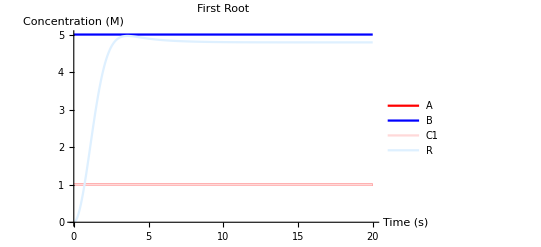

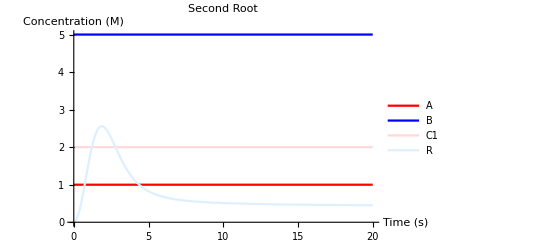

```mathematica
a=1;
b=5;
c=1;
EvalFirstRoot[a,b,c,100]
Roots[a*x^2-b*x+c==0,x][[2,2]]+0.0
EvalSecondRoot[a,b,c,100]
Roots[a*x^2-b*x+c==0,x][[1,2]]+0.0
PlotFirstRoot[a,b,c,20]
PlotSecondRoot[a,b,c,20]
```

3.23014

3.23014

0.104348

0.103195

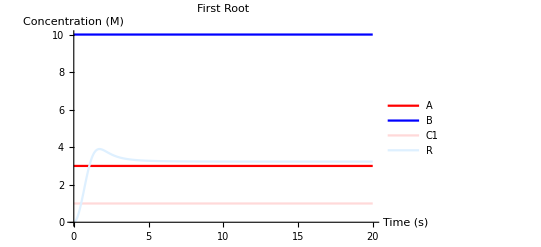

-Graphics-

```mathematica
a=3;
b=10;
c=1;
EvalFirstRoot[a,b,c,100]
Roots[a*x^2-b*x+c==0,x][[2,2]]+0.0
EvalSecondRoot[a,b,c,100]
Roots[a*x^2-b*x+c==0,x][[1,2]]+0.0
PlotFirstRoot[a,b,c,20]
PlotSecondRoot[a,b,c,20]
```

Tests that it works with some random intermediate species values. Tested all intermediate species with values 1 or 10 and none had any effect.

```mathematica
PlotDifConcs[Fc_,FAc_,FACc_,Sc_,SQc_,NUMc_,Tc_,TAc_]:=Module[ {rsys,sol},rsys=Flatten[{CRNsquare[SB,B],CRNconst[F,4],CRNmul[F,A,FA],CRNmul[FA,C1,FAC],CRNrsub[SB,FAC,S],CRNsqrt[S,SQ],CRNadd[B,SQ,NUM],CRNconst[T,2],CRNmul[T,A,TA],CRNdiv[NUM,TA,R]}];
sol=SimulateRxnsys[Join[rsys,{conc[A,1],conc[B,5],conc[C1,2],conc[F,Fc],conc[FA,FAc],conc[FAC,FACc],conc[S,Sc],conc[SQ,SQc],conc[NUM,NUMc],conc[T,Tc],conc[TA,TAc]}],100];
val=R[100]/.sol
]
```

```mathematica
Table[PlotDifConcs[a,b,c,d,e,f,g,h],{a,{1,10}},{b,{1,10}},{c,{1,10}},{d,{1,10}},{e,{1,10}},{f,{1,10}},{g,{1,10}},{h,{1,10}}]
```

{{{{{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}},{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}}},{{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}},{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}}}},{{{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}},{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}}},{{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}},{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}}}}},{{{{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}},{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}}},{{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}},{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}}}},{{{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}},{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}}},{{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}},{{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}},{{{4.56155,4.56155},{4.56155,4.56155}},{{4.56155,4.56155},{4.56155,4.56155}}}}}}}}

For inputs that are not valid the CRN still outputs a number because the networks still has values that go through it (an example below). We might be able to change the construction to accommodate the possibility of negative numbers or imaginary number by using a dual rail system. We can have the multiple rails represent the negative or imaginary part of the number.

```mathematica
EvalSecondRoot[2,3,4,100]
```

0.733252

## Part 2: Impossible computations with CRNs (10 points)

We want to find a non-negative continuous functions of non-negative real variables that cannot be computed by catalytic analog CRNs, using the one-variable : one-species signal representation. My first through for a function that would be hard to model would be something that has different behaviors at various parts of the function. I thought about the absolute value or modulus functions, but the absolute value will have no effect on non-negative real variables and the modulus function is not continuous. I then considered the sin and cos functions because they also seem like they have behavior that would be hard to find a way to compute using CRNs, but these have negative outputs; a function that I don’t think is possible to be modeled by CRNs is the absolute value of sin function because the shape and sharp turn seem like they would be hard to model and from a math point of view, the derivative of sin is cos so, from my understanding, it doesn’t seem like that works in the ODE dynamics equation.  This also made be think about the other forms of sin like trying to model it through e^i*pi*theta, but we can see that this also cannot be modeled because we have i that is imaginary and both e and pi that are irrational and not able to be exactly created by a CRN (just approximated). From this logic it would seem that a function like the area of circle from radius would also not work because of the need for pi, but if we can input irrational numbers like pi as constants than it could be fine.